# Displaying Lists

## S.M. Raihanul Bashir

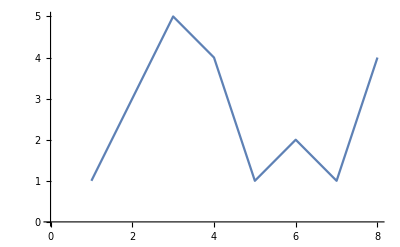

```mathematica
ListLinePlot[{1,3,5,4,1,2,1,4}]
```

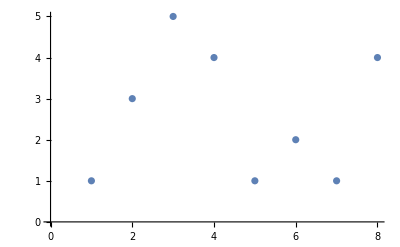

```mathematica
ListPlot[{1,3,5,4,1,2,1,4}]
```

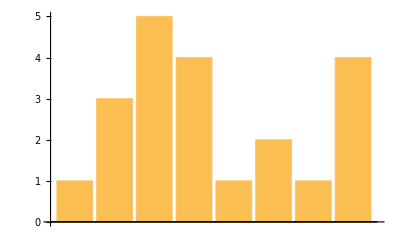

```mathematica
BarChart[{1,3,5,4,1,2,1,4}]
```

```mathematica
PieChart[{1,3,5,4}]
```

-Graphics-

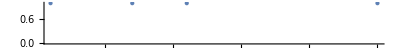

```mathematica
NumberLinePlot[{1,7,11,25}]
```

```mathematica
Column[{100,350,502,400}]
```

100
350
502
400

*** Lists can contain anything, including graphics.

```mathematica
{PieChart[Range[3]], PieChart[Range[5]]}
```

{-Graphics-,-Graphics-}

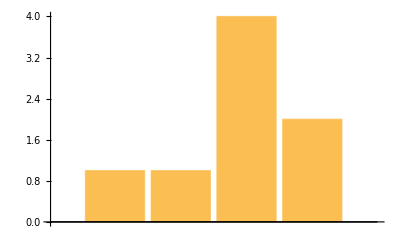
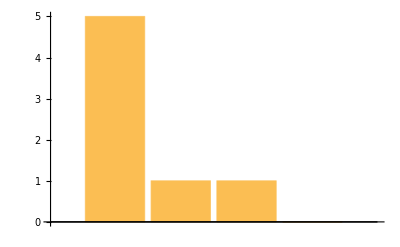
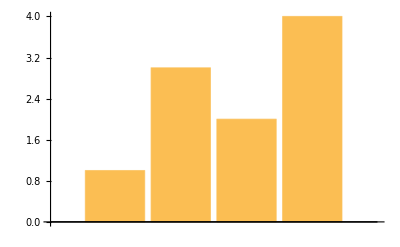

```mathematica
{BarChart[{1,1,4,2}],BarChart[{5,1,1,0}], BarChart[{1,3,2,4}]}
```

### Exercises:

1. Make a bar chart of {1, 1, 2, 3, 5}

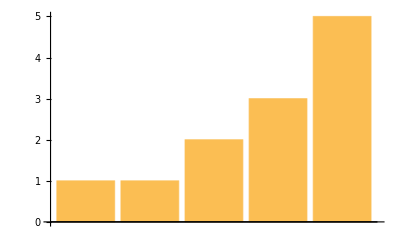

```mathematica
BarChart[{1,1,2,3,5}]
```

2. Make a pie chart of numbers from 1 to 10

```mathematica
PieChart[Range[10]]
```

-Graphics-

3. Make a bar chart of numbers counting down from 20 to 1

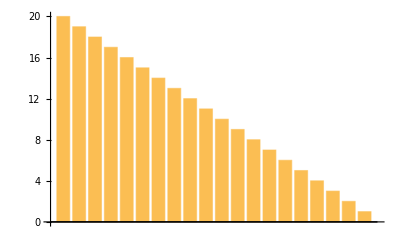

```mathematica
BarChart[Reverse[Range[20]]]
```

4. Display numbers from 1 to 5 in a column

```mathematica
Column[Range[5]]
```

1
2
3
4
5

5. Make a number line plot of the squares {1, 4, 9, 16, 25}.

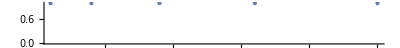

```mathematica
NumberLinePlot[{1,4,9,16,25}]
```

6. Make a pie chart with 10 identical segments, each of size 1

```mathematica
PieChart[{1,1,1,1,1,1,1,1,1,1}]
```

-Graphics-

7. Make a column of pie charts with 1, 2 and 3 identical segments

```mathematica
Column[{PieChart[{1}], PieChart[{1,1}], PieChart[{1,1,1}]}]
```

-Graphics-

8. Make a list of pie charts with 1, 2 and 3 identical segments

```mathematica
List[PieChart[{1}],PieChart[{1,1}], PieChart[{1,1,1}] ]
```

{-Graphics-,-Graphics-,-Graphics-}

9. Make a bar chart of the sequence 1, 2, 3, ..., 9, 10, 9, 8, 7, ..., 1

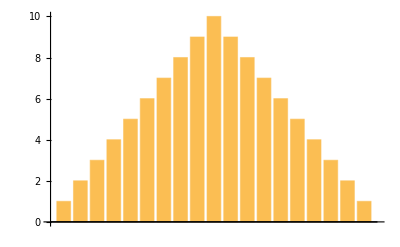

```mathematica
BarChart[Join[Range[10], Reverse[Range[9]]]]
```

10. Make a list of a pie chart, bar chart and line plot of the numbers from 1 to 10

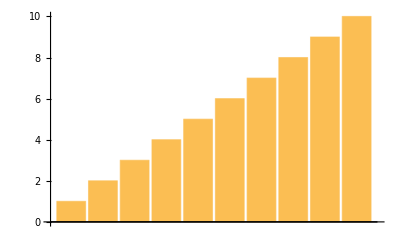
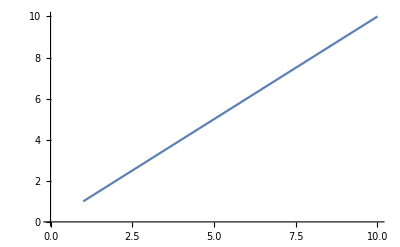
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
List[PieChart[Range[10]], BarChart[Range[10]], ListLinePlot[Range[10]]]
```

11. Make a list of a pie chart and a bar chart of {1, 1, 2, 3, 5, 8, 13, 21, 34, 55}

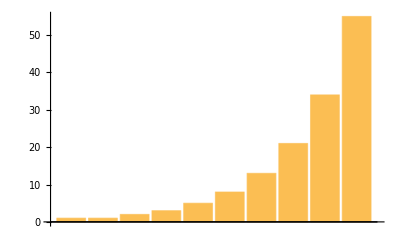
{-Graphics-,-Graphics-}

```mathematica
List[PieChart[Fibonacci[Range[10]]], BarChart[Fibonacci[Range[10]]]]
```

12. Make a column of two number line plots of {1, 2, 3, 4, 5}

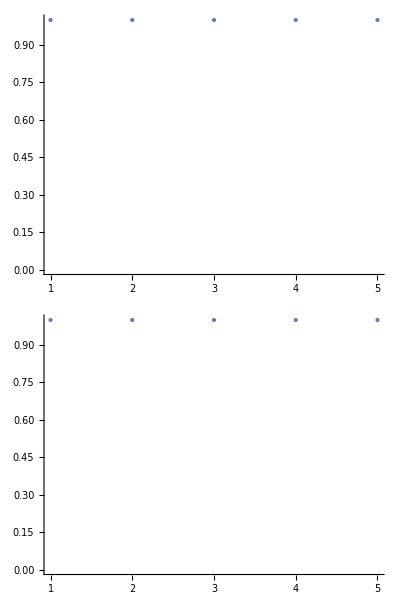

```mathematica
Column[{NumberLinePlot[Range[5]], NumberLinePlot[Range[5]]}]
```

13. Make a number line of fractions 1/2, 1/3, ... through 1/9

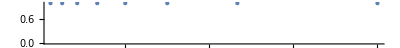

```mathematica
NumberLinePlot[{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9}]
```